```mathematica
OmegaZAMO=-kerr[[1,4]]/kerr[[4,4]]
OmegaZAMOjp=-metric[[1,4]]/metric[[4,4]]
```

(2 a M r)/(Σ (a^2+r^2+(2 a^2 M r Sin[θ]^2)/Σ))

(2 a M r (1+(M^3 r ϵ3)/Σ^2))/(Σ (a^2+r^2+(2 a^2 M r Sin[θ]^2)/Σ+(a^2 M^3 r ϵ3 (2 M r+Σ) Sin[θ]^2)/Σ^3))

```mathematica
it=OmegaZAMO/.ϵ3->0/.Δ->r^2-2M r+a^2/.Σ->r^2+a^2(Cos[θ])^2//Simplify
itjp=OmegaZAMOjp/.Δ->r^2-2M r+a^2/.Σ->r^2+a^2(Cos[θ])^2//Simplify
```

(2 a M r)/(a^2 (a^2+r^2) Cos[θ]^2+r (a^2 r+r^3+2 a^2 M Sin[θ]^2))

(2 a M r (1+(M^3 r ϵ3)/((r^2+a^2 Cos[θ]^2)^2)))/((r^2+a^2 Cos[θ]^2) (a^2+r^2+(2 a^2 M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)+(a^2 M^3 r ϵ3 (r (2 M+r)+a^2 Cos[θ]^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^3)))

```mathematica
god=FullSimplify[it//.{r->M+Sqrt[M^2-a^2],M->1}]
```

-(-1+√(1-a^2))/(2 a)

```mathematica
rp=1+Sqrt[1-a^2]
god2=a/(2*rp)
FullSimplify[god-god2]
```

1+√(1-a^2)

a/(2 (1+√(1-a^2)))

0

```mathematica
it2=OmegaZAMO/.Δ->r^2-2M r+a^2/.Σ->r^2+a^2(Cos[θ])^2//Simplify
it2jp=OmegaZAMOjp/.Δ->r^2-2M r+a^2/.Σ->r^2+a^2(Cos[θ])^2//Simplify
```

(2 a M r)/(a^2 (a^2+r^2) Cos[θ]^2+r (a^2 r+r^3+2 a^2 M Sin[θ]^2))

(2 a M r (1+(M^3 r ϵ3)/((r^2+a^2 Cos[θ]^2)^2)))/((r^2+a^2 Cos[θ]^2) (a^2+r^2+(2 a^2 M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)+(a^2 M^3 r ϵ3 (r (2 M+r)+a^2 Cos[θ]^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^3)))

```mathematica
bottomjp=a^2+r^2+(2 a^2 M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)+(a^2 M^3 r ϵ3 (r (2 M+r)+a^2 Cos[θ]^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^3)
```

a^2+r^2+(2 a^2 M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)+(a^2 M^3 r ϵ3 (r (2 M+r)+a^2 Cos[θ]^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^3)

```mathematica
FullSimplify[it2jp//.{ϵ3->a,θ->Pi/2}]
FullSimplify[it2//.{ϵ3->a,θ->Pi/2}]
```

(2 a M (a M^3+r^3))/(r^6+a^3 M^3 (2 M+r)+a^2 r^3 (2 M+r))

(2 a M)/(r^3+a^2 (2 M+r))

```mathematica
plot2=FullSimplify[it2//.{M->1,a->1}]
```

(2 r)/((1+r^2) (r^2+Cos[θ]^2)+2 r Sin[θ]^2)

```mathematica
it2jp//.{r->1*rp,M->1,a->.99,ϵ3->-2,θ->Pi/2}
```

-1.63173

```mathematica
plot2=FullSimplify[it2//.{r->rp,M->1,a->1}]
plot2jp=FullSimplify[it2jp//.{r->1*rp,M->1,a->.99,ϵ3->-10}]
```

1/2

-((0.+4.89808×10^15 ⅈ) (-2.11808+Cos[θ]^2) (4.77503+Cos[θ]^2))/((0.+9.16393×10^15 ⅈ)-(0.+6.58776×10^16 ⅈ) Cos[2 θ]-(0.+4.5036×10^15 ⅈ) Cos[4 θ]+(1.+0. ⅈ) Sin[4 θ])

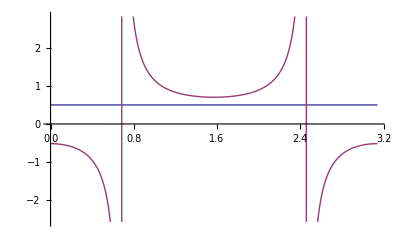

```mathematica
Plot[{plot2,plot2jp},{θ,0,Pi}]
```

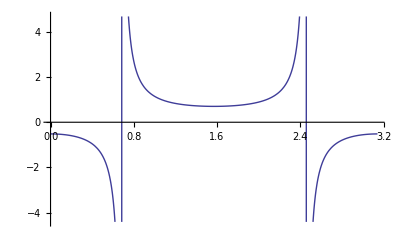

```mathematica
Plot[{plot2jp},{θ,0,Pi}]
```

```mathematica
2200/43.
```

51.1628

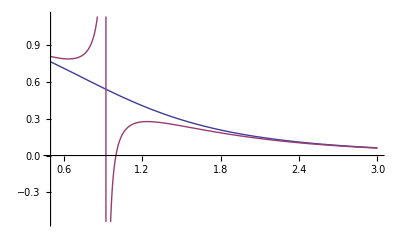

```mathematica
Plot[{plot2,plot2jp},{r,.5,3}]
```